# Windowed Incremental Online Statistics

## Extracting Models from Data, One Observation at a Time

Brian Beckman

11 May 2024

We calculate descriptive statistics—count, mean, unbiased variance—both overall and in a sliding window, of sequences of numerical data. The statistics calculator is written as a foldable accumulator function, decoupling calculation from iteration. Exactly the same stateless accumulator function works over data distributed over space in memory or tables, or over time in asynchronous or lazy streams. Foldable accumulator functions can be tested independently of data source, say over ground-truth test data, then later deployed in harsh asynchronous environments with high assurance, often without even being recompiled.

The solution at the end of this notebook has been implemented in C, C++, Python, and Clojure and deployed in mission-critical web applications and embedded applications. It runs in O(w) space, where w is the width of the window, and in O(1) time. Contrast to more obvious solutions that run in O(w) time.

## Prelude: Running Count

For ground truth, we want a fixed but random sequence of data. The following is a sample of length 10 from the standard normal distribution—mean zero, standard deviation one:

```mathematica
zs = {-0.178654,0.828305,0.0592247,-0.0121089,-1.48014,-0.315044,-0.324796,-0.676357,0.16301,-0.858164};
```

Fold has three arguments: an accumulator function, an initial state, and a sequence of data. All variations of Fold—over asynchronous streams, over on-demand (lazy) streams, over tables, lists, arrays—have exactly the same signature as Fold. Wolfram’s Fold is equivalent to reduce in Python and to std::accumulate in C++.

```mathematica
ClearAll[cume];
cume[n_,z_]:=n+1;
Fold[cume,0,zs]
```

10

The first argument of the accumulator function, cume, is a circulating state, kept externally to the function. Above, the circulating state is n. The caller must feed two arguments to cume: the prior value n of the circulating state and a new observation z. The caller receives the posterior value of the state, n+1.

To see all intermediate results, use FoldList:

```mathematica
FoldList[cume,0,zs]
```

{0,1,2,3,4,5,6,7,8,9,10}

### LEFT FOLD

Wolfram’s documentation for Fold includes an example that explains this operator symbolically. The following should be self-explanatory:

```mathematica
Fold[f,z,{a,b,c,d}]
```

f[f[f[f[z,a],b],c],d]

Fold first computes f[z,a], then feeds the result—the posterior value of the circulating state—back into f, computing f[f[z,a],b], and so on. More concisely, Fold iteratively applies the binary function f to the sequence {a,b,c,d}. That’s why we say Fold decouples calculation from iteration. Fold places no restriction on its accumulator-function argument f other than that it accept an argument of the type T_z of z in its first position, an argument of the type T_a of any of a,b,c,d, in its second position, and produces a result of type T_a.

### RIGHT FOLD

It is important to know that there is a dual: the right fold. Left and Right folds can behave differently on lazy lists, so be on the lookout! We use only left fold in this document.

```mathematica
Fold[{x,y}↦f[y,x],z,{a,b,c,d}]
```

f[d,f[c,f[b,f[a,z]]]]

## Running Mean

Write x for the mean-so-far, and write a new accumulator function that computes the running mean. Its circulating state is a tuple including the running mean x, the running count n, and the running sum. The following new accumulator function computes the new values of all three state variables in the obvious way. Note that all three state variables—members of the state tuple—are necessary to track the running mean calculated this way. We relieve that situation shortly below.

```mathematica
ClearAll[cume];
cume[{x_,n_,sum_},z_]:=
{(sum+z)/(n+1),n+1,sum+z};
Fold[cume,{0,0,0},zs]
```

{-0.279472,10,-2.79472}

Check against Mathematica built-in.

```mathematica
Mean[zs]
```

-0.279472

Notice how the mean stabilizes as data accumulate, here over a longer and random sample:

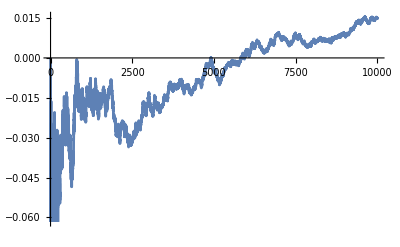

```mathematica
ListLinePlot[#⟦1⟧&/@FoldList[cume,{0,0,0},RandomVariate[NormalDistribution[],10000]]]
```

## Preferable Form

Here is a preferable form with one fewer quantity in the circulating state tuple. This form is so powerful that we state it as a mantra or slogan:

Compute the new value as sum of the old value and a correction that depends only on old values and the single observation z.

We will strive for this form in everything that follows. It is the essential feature of all recurrent filter algorithms including the famous Kalman filter.

The right-hand side of the recurrence z̄←z̄+K×(z-z̄), z̄ here standing for the running mean, depends only on old values and the new observation z. The recurrence is not an equation, but it is shorthand the following equation:

(z̄)_(n+1)=(z̄)_n+K×(z_(n+1)-(z̄)_n)=x+K×(z_(n+1)-x).

```mathematica
ClearAll[cume];
cume[{x_,n_},z_]:=
With[{K=1/(n+1)},
{x+K(z-x),n+1}];
Fold[cume,{0,0},zs]
```

{-0.279472,10}

We prefer this form because (1) it separates old quantities on the right (except for the new datum, z) from new quantities on the left, and (2) it is easy to memorize because it is an affine update: the old estimate plus a correction written as a gain K times the residual z-z̄. The residual is the difference between the new observation and the old mean-so-far. It measures how far off is the new observation from the mean-so-far.

To prove this formula z̄+K×(z-z̄) correct, we need only show that it equals (sum+z)/(n+1), which is obviously the new mean. Write z̄, the old mean, as (z̄(n+1))/(n+1)=(n z̄+z̄)/(n+1) via the venerable trick of multiplying the numerator and denominator of a ratio by the same number, and write z̄+K×(z-z̄)=(n z̄+z̄)/(n+1)+(z-z̄)/(n+1)=(sum+z)/(n+1), noting that the old sum is n z̄. I think this is beautiful. The same reasoning will help us derive many more sophisticated formulas, up-to-and-including the Kalman update.

For another twist on the proof above, let Mathematica do the work. The Kalman-like form x+K(z-x) is equal to the obvious form (n x+z)/(n+1) when n+1≠ 0, now letting x stand for the old mean z̄ because x is a little easier to read.

```mathematica
Solve[x+K(z-x)==(n x+z)/(n+1),K]
```

{{K→1/(1+n)}}

## Running Variance

### Definitions

Variance is the sum of squared residuals against the running mean, divided by the count less one. The “count less one” is Bessel's correction, not explained here.

```mathematica
Variance[zs]
```

0.395183

Variance is also the square of standard deviation.

```mathematica
StandardDeviation[zs]^2==Variance[zs]
```

True

The sum of squared residuals,

Σ_n=^def∑_(i=1)^n (z_i-(z̄)_n)^2

is the variance times the length-less-one:

```mathematica
Variance[zs]*(Length[zs]-1)
```

3.55665

The sum of squared residuals will be a cornerstone quantity for all future calculations. Here is another look at it, via the anonymous function (#-μ)^2& applied via /@.

```mathematica
With[{μ=Mean[zs]},
Plus@@((#-μ)^2&/@zs)]
```

3.55665

### Requirement

We require an incremental, running variance that does not refer to future observations—even indirectly, through the eventual mean (z̄)_n—and does not store the entire past, only a summary of constant size.

The definition above explicitly refers to the past history. It seems, at first glance, impossible to compute the variance without keeping the entire history. But it possible, and we’ll get there in baby steps.

### Brute-Force Variance (doesn’t meet requirements)

The following accumulates variance directly from the definition, useful for numerical checks. However, it assumes we know the length and mean of the entire sequence zs ahead of time, so it does not meet the requirement of being incremental. It also needs computer memory for the entire sequence zs, which is of variable,  unknown, or infinite length, so does not meet the requirement of constant memory.

Re-use the variable zs, now for a shorter sequence of ground-truth data, convenient for checking arithmetic in one’s head.

```mathematica
ClearAll[zs];zs={55,89,144};
```

```mathematica
Variance[zs]//N
```

2017.

Hand-calculated mean:

```mathematica
(55+89+144)/3.
```

96.

Hand-calculated variance = SSR (sum of squared residuals) / (n-1):

```mathematica
((55-96.)^2+(89-96.)^2+(144-96.)^2)/2.
```

2017.

Now, we’ll write a truly nasty accumulator function to produce the final variance. It’s nasty because it refers to the entire sequence through the variable zs.

```mathematica
ClearAll[cume];
cume[var_,z_]:=var+(z-Mean[zs])^2/(Length[zs]-1);
FoldList[cume,0.,zs]
```

{0.,840.5,865.,2017.}

It’s even nastier because the intermediate variances are not valid. They do not refer to the “mean-so-far”—the incremental running mean, but to the final mean.

### School Variance (meets requirements)

The following is much better, exploiting the “school formula,” proved by expanding the square. Letting (z̄)_n=x, incremental running mean, the following yields the sum of squared residuals, ssq:

∑_(i=1)^n (z_i-(z̄)_n)^2=(∑_(i=1)^n z_i^2)-n (z̄)_n^2

This is very nice because we can maintain ∑_(i=1)^n z_i^2 incrementally, just as we maintain the running sum, ∑_(i=1)^n z_i, one observation at a time.

The Variance is ssq divided by n-1 when n>1. When n=1, variance must be zero because there is no dispersion when there is only one datum. Concatenate the variance and ssq to the circulating state, making a 4-tuple, and write:

```mathematica
ClearAll[cume];
cume[{var_,ssq_,x_,n_},z_]:=
With[{n2=n+1},
With[{K=1/n2},
With[{x2=x+K(z-x),ssq2=ssq+z^2},
{(ssq2-n2 x2^2)/Max[1,n],ssq2,x2,n2}]]];
FoldList[cume,{0,0,0,0},zs]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 3025 | 55 | 1
578 | 10946 | 72 | 2
2017 | 31682 | 96 | 3)

The variance computed this way is incremental and runs in constant memory, though it is not yet a recurrence, i.e., old value plus a correction.

This school variance tracks three auxiliary quantities: the sum of squares ssq, the running mean x, and the count n. Note, for the future, that ssq grows quickly, inviting numerical issues. We’ll mitigate that shortly.

### Recurrent Variance (meets requirements)

Though it is incremental, the school variance isn’t a recurrence. A recurrence, in our preferred form, expresses the new variance as the old variance plus a correction, where the correction depends only on old values and the new datum z. Start with a recurrence for the sum of squared residuals, ssq, Σ_n=^def∑_(i=1)^n (z_i-(z̄)_n)^2:

Σ←Σ+n/(n+1)(z-z̄)^2

The form in Recurrence 4 is an abbreviation for the upcoming Equation 5. The abbreviation is precise under the rule that all accumulated quantities, namely z̄ and Σ, on the right of the recurrence arrow, are old—have implicit subscript n. Only the datum z is new—with subscript n+1, on the right of the recurrence arrow.

Σ_(n+1)=Σ_n+n/(n+1)(z_(n+1)-(z̄)_n)^2

#### Symbolic Proof

Here’s the old ssq from the School formula:

S_n=∑_(i=1)^n z_i^2-n(z̄)_n^2

Here’s the new ssq via the same formula:

S_(n+1)  =  ∑_(i=1)^(n+1) z_i^2-(n+1)(z̄)_(n+1)^2

Let the sum of squares—not the sum of squared residuals—s z_n^2= sz2[n] be ∑_(i=1)^n z_i^2. Note that sz_(n+1)^2=sz_n^2+z^2, and also that (n+1)(z̄)_(n+1)=n (z̄)_n+z. Those obvious (but beautiful) equalities are enough to effect the proof.

Transcribe Equation 6.

```mathematica
ClearAll[s,zb,zbar];
s[n_]:=sz2[n]-n zbar[n]^2
```

Transcribe the “obvious equalities” above.

```mathematica
rulez$={sz2[1+n]-sz2[n]->z^2,zbar[1+n]->n/(n+1) zbar[n]+z/(n+1)};
```

Note that the rules don’t do much to the definition of s[n].

The rules instantly yield the correction terms in Recurrence 4 and Equation 5.

```mathematica
s[n+1]-s[n]//.rulez$//FullSimplify
```

(n (z-zbar[n])^2)/(1+n)

#### Proof by Hand

Remember the “obvious equalities.”

s z_(n+1)^2=s z_n^2+z^2

(n+1)(z̄)_(n+1)=n(z̄)_n+z

Expand out the definition of S_(n+1) and employ the “obvious equalities”:

S_(n+1)=[sz_(n+1)^2-(n+1)(z̄)_(n+1)^2]=[sz_n^2+z^2]-(1/(n+1)[(n+1)(z̄)_(n+1)])^2    =    [s z_n^2+z^2]-(1/(n+1)[n(z̄)_n+z])^2

Expand the second term:

S_(n+1)=s z_n^2+z^2-n^2/(n+1)(z̄)_n^2-(2n)/(n+1)z (z̄)_n-1/(n+1)z^2

Add and subtract a term—another venerable trick—to isolate the prior value of S_n and prepare other terms for cancelation:

=[s z_n^2-n (z̄)_n^2]+n(n+1)/(n+1) (z̄)_n^2+(n+1)/(n+1)z^2-n^2/(n+1)(z̄)_n^2-(2n)/(n+1)z (z̄)_n-1/(n+1)z^2

Cancel terms and complete the square:

=[s z_n^2-n (z̄)_n^2]+n/(n+1) (z̄)_n^2-(2n)/(n+1)z (z̄)_n+n/(n+1)z^2

S_(n+1)=S_n+n/(n+1)(z- (z̄)_n)^2

#### Equivalence to Welford’s

Welford’s famous recurrence is

Σ←Σ+(z-(z̄)_n)(z-(z̄)_(n+1))

where (z̄)_n is the last estimate of the mean and (z̄)_(n+1) is the new or current estimate. The correction term on the right of Recurrence 8 is exactly equal to the correction term on the right of recurrence 4.

```mathematica
(z-zbar[n])(z-zbar[n+1]//.rulez$//FullSimplify)
```

(n (z-zbar[n])^2)/(1+n)

We won’t write out the algebraic manipulations, but it’s good practice.

Welford's is easier to memorize than is Recurrence 4, but its right-hand side depends on both the old mean (z̄)_n and the new mean (z̄)_(n+1), whereas we always want right-hand sides that depend only on old values (except for new datum z) because such right-hand sides require fewer intermediate variables. Notice the following, using Welford’s, has three levels of With because ssr2 depends on two means and we must precompute the new mean x2:

```mathematica
ClearAll[cume];
cume[{var_,x_,n_},z_]:=
With[{K=1/(n+1)},
With[{x2=x+K(z-x)},
With[{ssr2=(n-1)var+(z-x)(z-x2)},
{ssr2/Max[1,n],x2,n+1}]]];
FoldList[cume,{0,0,0},zs]//MatrixForm
```

(0 | 0 | 0
0 | 55 | 1
578 | 72 | 2
2017 | 96 | 3)

#### Folding It

Recurrence 4 lets us get rid of one level of With, one level of dependency:

```mathematica
ClearAll[cume];
cume[{var_,x_,n_},z_]:=
With[{K=1/(n+1)},
With[{x2=x+K(z-x),
ssr2=(n-1) var+K n(z-x)^2},
{ssr2/Max[1,n],x2,n+1}]];
FoldList[cume,{0,0,0},zs]//MatrixForm
```

(0 | 0 | 0
0 | 55 | 1
578 | 72 | 2
2017 | 96 | 3)

## Windowed Statistics

Sometimes, we want the mean and variance of a limited amount of the past, say over a window of length w>=0.

```mathematica
Manipulate[
Grid[Table[With[{l=i-w+1},Piecewise[{{Item[j,Background->LightBlue], j<l}, {Item[j,Background->Yellow], j≤i}, {j, True}}]],{i,n+w},{j,n}],Frame->All],
{{n,10},5+Range[100]},
{{w,3},Range[n+1]-1,Appearance->"Labeled"}]
```

## Foldable

runningStatsFoldable is a a foldable accumulator function that effects windowed statistics. Its circulating state carries extra information for pedagogy and convenience. It’s possible to make the interface much tighter. The derivation of its formulae are written in comments. The specific example data in this section are taken from other deployments of this code in C and Python. In the next section, we add some checks of the results against Mathematica’s built-ins.

```mathematica
On[Assert];
```

```mathematica
ClearAll[runningStatsFoldable];
Module[{u,j,mnp1,mjp1,mw,vnp1,vjp1,vw,cbuf=ConstantArray[0,3],zj},
runningStatsFoldable[w_][{
_,(* j, count of elements left of the window, j>=0 *)
n_,(* index of the current datum; start at 0 *)

_,(* u, elements in the window, 0<=u<=w *)
_,(* z, new datum circulated for convenience *)
_,(* Subscript[z, j], datum evicted from the window *)

mn_,(* mean of all data *)
mj_,(* mean of data to the left of the window *)
_,(* mean of data in the window *)

vn_,(* variance of all data *)
vj_,(* variance of data to the left of the window *)
_},(* variance of data in the window *)
z_]:=(
(* there are five recurrent inputs n, mn, mj, vn, vj *)
(*     and two actionable outputs mw and vw *)
(*     in the circulating-state vector. The rest of the items *)
(*     are auxilaries for verifying and debugging. *)

(* window starts overlapping data by 1 cell, then by 2 cells *)
(* eventually window becomes flush left, then advances into *)
(* the data, leaving evicted data to its left *)

(* datum at the right of the window -- datum to be evicted *)
zj=cbuf⟦w⟧;
(* rotate zj to the left of the window *)
cbuf=RotateRight[cbuf,1];
(* replace zj with z *)
cbuf⟦1⟧=z;

(* window starts containing one datum when n is 0 *)
(* eventually, when n is w-1, window is flush left *)

(* j = elements to left of window, 0 when flush left *)
(*     then > 0 thereafter if w < N *)
j=Max[0,n-w+1];

(* u = number of data in the window *)
(* starts at 1, becomes 2, ..., w *)
(* becomes w when j is flush left and stays w *)
u=n-j+1; Assert[u<=w];

(* mn = prior mean of all data before z -- recurrent input *)
(* mnp1 = posterior mean of all data including z *)
(* this is our normal gain times residual calc *)
mnp1=mn+(z-mn)/(n+1);

(* mj = prior mean of data left of window -- recurrent input*)
(* mjp1 = posterior mean of data left of the window *)
mjp1=If[j>0,mj+(zj-mj)/j,0];

(* mw = posterior mean of data in window -- output *)
mw=((n+1)mnp1-j mjp1)/u;

(* vn = prior variance of all data -- recurrent input *)
(* posterior variance of all data via Recurrence 4 *)
vnp1=((n-1)vn+n/(n+1)(z-mn)^2)/Max[1,n];

(* vj = prior variance of data left of window -- recurrent input *)
(* vjp1 = posterior variance of data to left of window *)

(* increase by scaled residual of the evicted datum vj *)
(* will be zero until window moves off of flush left *)
(* so it is safe to multiply it later by a negative n-w *)
vjp1=If[j>1,(j-2)/(j-1)vj+1/j(zj-mj)^2,0];

(* vw = posterior variance of data in window -- output *)

(* by three applications of the school formula *)
(* Subscript[n, Bessel] Subscript[v, n+1] = ∑_(i=1)^(n+1) (Subscript[z, i])^2-(n+1)Subscript[z̄, n+1] ; ditto for j *)

(* The first two terms in the numerator combine to equal *)
(*   the sum of squared data (not residuals) in the window *)

(* the third term in the numerator is the school correction *)
(* for the window TODO make it Welford's or Recurrence 4 *);
vw=((n vnp1+(n+1)mnp1^2)-((n-w)vjp1+j mjp1^2)-u mw^2)/Max[1,u-1];
(* RETURN VALUE *)
{j,n+1,u,z,zj,
mnp1,mjp1,mw,
vnp1,vjp1,vw
})]; 
With[{data={0.857454,0.312454,0.705325,0.839363,1.63781,0.699257,-0.340016,-0.213596,-0.0418609,0.054705}},
Grid[
Prepend[FoldList[runningStatsFoldable[3],{0,0,0,0,0,0,0,0,0,0,0},data],
{"j","n+1","u","z","z_j","μ'","μ'_j","μ'_w","υ'","υ'_j","υ'_w"}],Frame->All]]
```

j | n+1 | u | z | z_j | μ' | μ'_j | μ'_w | υ' | υ'_j | υ'_w
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0.857454 | 0 | 0.857454 | 0 | 0.857454 | 0. | 0 | 0.
0 | 2 | 2 | 0.312454 | 0 | 0.584954 | 0 | 0.584954 | 0.148513 | 0 | 0.148513
0 | 3 | 3 | 0.705325 | 0 | 0.625078 | 0 | 0.625078 | 0.079086 | 0 | 0.079086
1 | 4 | 3 | 0.839363 | 0.857454 | 0.678649 | 0.857454 | 0.619047 | 0.0642035 | 0 | 0.0749912
2 | 5 | 3 | 1.63781 | 0.312454 | 0.870481 | 0.584954 | 1.06083 | 0.232151 | 0.148513 | 0.254169
3 | 6 | 3 | 0.699257 | 0.705325 | 0.841944 | 0.625078 | 1.05881 | 0.190607 | 0.079086 | 0.256338
4 | 7 | 3 | -0.340016 | 0.839363 | 0.673092 | 0.678649 | 0.665684 | 0.358415 | 0.0642035 | 0.978794
5 | 8 | 3 | -0.213596 | 1.63781 | 0.562256 | 0.870481 | 0.0485483 | 0.40549 | 0.232151 | 0.321562
6 | 9 | 3 | -0.0418609 | 0.699257 | 0.495132 | 0.841944 | -0.198491 | 0.395354 | 0.190607 | 0.0223952
7 | 10 | 3 | 0.054705 | -0.340016 | 0.45109 | 0.673092 | -0.0669173 | 0.370824 | 0.358415 | 0.0184672

## Random Data, Checked

The solution does not work when the window size is zero, but is robust even in the nonsensical case of the window’s being longer than the data.

```mathematica
DynamicModule[{u,j,mnp1,mjp1,mw,vnp1,vjp1,vw,cbuf,zj,
ndata=16,w=6,data,cume},
data=N@RandomReal[{-100,100},ndata];
cbuf=ConstantArray[0,w];
cume[{_,n_,_,_,_,mn_,mj_,_,vn_,vj_,_},z_]:=(
zj=cbuf⟦w⟧;cbuf=RotateRight[cbuf,1];cbuf⟦1⟧=z;
j=Max[0,n-w+1];u=n-j+1;
mnp1=mn+(z-mn)/(n+1);mjp1=If[j>0,mj+(zj-mj)/j,0];
mw=((n+1)mnp1-j mjp1)/u;
vnp1=((n-1)vn+n/(n+1)(z-mn)^2)/Max[1,n];
vjp1=If[j>1,(j-2)/(j-1)vj+1/j(zj-mj)^2,0];
vw=((n vnp1+(n+1)mnp1^2)-(j mjp1^2+(n-w)vjp1)-u mw^2)/Max[1,u-1];
Assert[0===Chop[mjp1-If[j>0,Mean[data⟦1;;j⟧],0]]];
Assert[0===Chop[mw-Mean[data⟦j+1;;n+1⟧]]];
Assert[0===Chop[vjp1-If[j>1,Variance[data⟦1;;j⟧],0]]];
Assert[0===Chop[vw-If[u>1,Variance[data⟦j+1;;n+1⟧],0]]];
{j,n+1,u,z,zj,
mnp1,mjp1,mw,
vnp1,vjp1,vw});
Manipulate[
(ndata=dataLen;w=windowLen;cbuf=ConstantArray[0,w];Grid[
Prepend[FoldList[cume,{0,0,0,0,0,0,0,0,0,0,0},data],
{"j","n+1","u","z","z_j","μ_(n + 1)","μ_j","μ_w","υ_(n + 1)","υ_j","υ_w"}],Frame->All]),
{dataLen,{16,Sequence@@Range[10,40]}},
{windowLen,{6,Sequence@@Range[1,40]}},
Button["RANDOMIZE!",
data=N@RandomReal[{-100,100},ndata]]
]]
```